```mathematica
ClearAll["Global`*"]
```

```mathematica
tableS = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\SeriesCircut_2019_09_03_15_08_01.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtableS = Delete[tableS, 1];
```

```mathematica
ZparallelRC[R_, C_, ω_] := (R×1/(ⅈ×ω×C))/(R+1/(ⅈ×ω×C))
```

```mathematica
ZparallelRL[R_,L_,ω_]:=(R×ⅈ×ω×L)/(R+ⅈ×ω×L)
```

```mathematica
Zparallel3[R1_, R2_, R3_]:= (R1×R2×R3)/(R1×R2+R2×R3+R3×R1)
```

```mathematica
ZS[ω_,C0_,L_,Rp_,Cp_]:=50+1/(ⅈ×ω×C0)+Zparallel3[50×10^3, (ⅈ×ω×L+0.5+ZparallelRL[Rp,0.0011,ω]), (1/(ⅈ×ω×Cp))]
```

```mathematica
Uin[ω_,C0_,L_,Rp_,Cp_]:=2*Re[Abs[Zparallel[46.5, 25*10^-12, 2π×ω]]/Abs[ZS[2π×ω,C0,L,Rp,Cp]]]
```

```mathematica
fitS = FindFit[newtableS, Uin[ω,C0,L,Rp,Cp], {{C0,150×10^-12},{L, 2.03×10^-3},{Rp,160}, {Cp, 10^-11}}, ω, MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{C0→1.61773×10^-10,L→0.00203202,Rp→163.457,Cp→4.30931×10^-11}

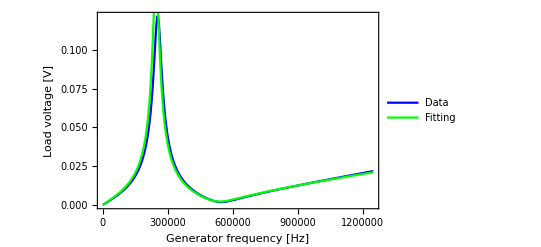

```mathematica
Legended[Show[ListLinePlot[newtableS, PlotStyle->Blue, PlotRange->Full],
Plot[Uin[ω,C0,L,Rp,Cp]/.fitS,{ω,Min[newtableS[[All,1]]],Max[newtableS[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->Full, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

```mathematica
tableP = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\ParallelCircut_2019_09_03_15_23_37.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtableP = Delete[tableP,1];
```

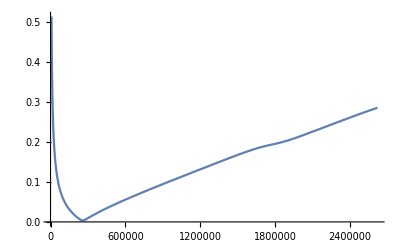

```mathematica
ListLinePlot[newtableP]
```

```mathematica
ZP[ω_]:=50+Zparallel[46.5, 25×10^-12, ω]+Zparallel2[(ⅈ×ω×9.83*10^-7+Zparallel[4.63×10^5, 1.52*10^-10, ω]+43.6),(Zparallel3[8.1×10^6, (ⅈ×ω×3.13*10^-3+0.61), (1/(ⅈ×ω×2.8*10^-11))])]
```

```mathematica
UinP[ω_]:=2*Re[Abs[Zparallel[46.5, 25*10^-12, 2π×ω]]/Abs[ZP[2π×ω]]]
```

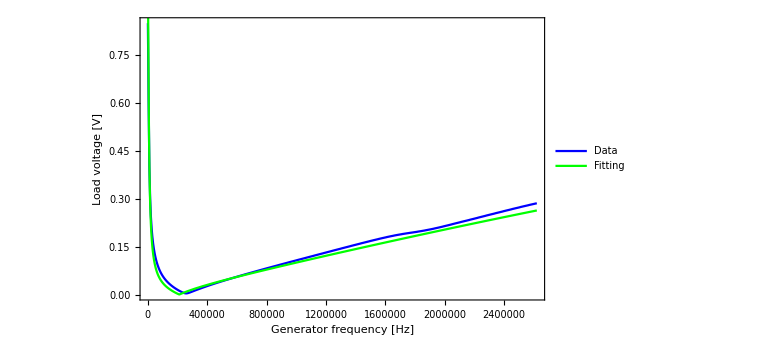

```mathematica
Legended[Show[ListLinePlot[newtableP, PlotStyle->Blue, PlotRange->Full],
Plot[UinP[ω],{ω,Min[newtableP[[All,1]]],Max[newtableP[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->Large, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

```mathematica
table1 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\IncompleteConnectionPrecise1_2019_09_03_16_14_54.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
table2=Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\IncompleteConnectionPrecise2_2019_09_03_16_26_49.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
table3=Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\IncompleteConnectionPrecise3_2019_09_03_16_45_44.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable1=Delete[table1, 1];
```

```mathematica
newtable2=Delete[table2, 1];
```

```mathematica
newtable3=Delete[table3, 1];
```

```mathematica
Z1[ω_]:=46.5+Zparallel2[(ⅈ×ω×9.83*10^-7+ Zparallel3[8.1×10^6, (ⅈ×ω×3.13*10^-3+0.61), (1/(ⅈ×ω×2.8*10^-11))]+Zparallel[4.63×10^5, 150*10^-9, ω]+50),(ⅈ×ω×5.39*10^-7+Zparallel[3.28*10^7, 1.5*10^-9, ω]+5.77)]+Zparallel[46.5, 25×10^-12, ω]
Uin1[ω_]:=2*Re[Abs[Zparallel[46.5, 25*10^-12, 2π×ω]]/Abs[Z1[2π×ω]]]
```

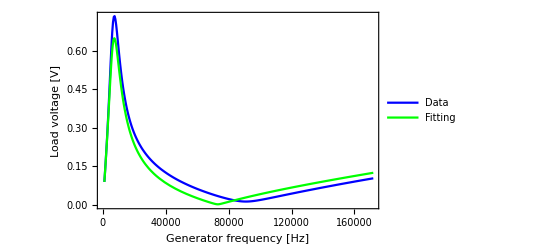

```mathematica
Legended[Show[ListLinePlot[newtable1, PlotStyle->Blue, PlotRange->Full],
Plot[Uin1[ω],{ω,Min[newtable1[[All,1]]],Max[newtable1[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->Full, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

```mathematica
Z2[ω_]:=46.5+Zparallel2[(ⅈ×ω×9.83*10^-7+ Zparallel3[8.1×10^6, (ⅈ×ω×3.13*10^-3+0.61), (1/(ⅈ×ω×2.8*10^-11))]+Zparallel[4.63×10^5, 150*10^-12, ω]+50),(ⅈ×ω×5.39*10^-7+Zparallel[3.28*10^7, 1.5*10^-9, ω]+5.77)]+Zparallel[46.5, 25×10^-12, ω]
Uin2[ω_]:=2*Re[Abs[Zparallel[46.5, 25*10^-12, 2π×ω]]/Abs[Z2[2π×ω]]]
```

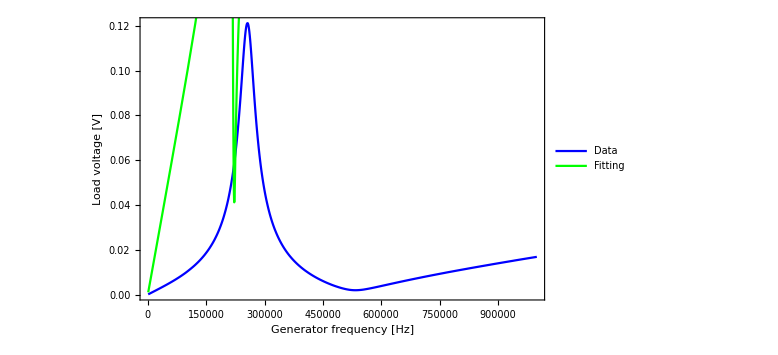

```mathematica
Legended[Show[ListLinePlot[newtable2, PlotStyle->Blue, PlotRange->Full],
Plot[Uin2[ω],{ω,Min[newtable2[[All,1]]],Max[newtable2[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->Large, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

```mathematica
Z3[ω_]:=46.5+Zparallel2[(ⅈ×ω×5.39*10^-7+ Zparallel3[8.1×10^6, (ⅈ×ω×3.13*10^-3+0.61), (1/(ⅈ×ω×2.8*10^-11))]+Zparallel[3.28×10^7, 1.5*10^-9, ω]+5),(ⅈ×ω×9.8*10^-7 3+Zparallel[4.63*10^5, 150*10^-12, ω]+5.77)]+Zparallel[46.5, 25×10^-12, ω]
Uin3[ω_]:=2*Re[Abs[Zparallel[46.5, 25*10^-12, 2π×ω]]/Abs[Z3[2π×ω]]]
```

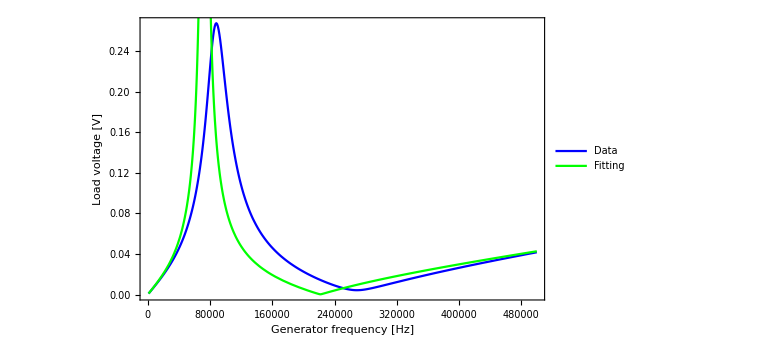

```mathematica
Legended[Show[ListLinePlot[newtable3, PlotStyle->Blue, PlotRange->Full],
Plot[Uin3[ω],{ω,Min[newtable3[[All,1]]],Max[newtable3[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->Large, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```